```mathematica
S :=16
S
Sc := S/2
```

16

```mathematica
cr:={{0,1},{0,0}}
```

```mathematica
an:= {{0,0},{1,0}}
n=.
```

```mathematica
cr ;
```

```mathematica
an ;
```

```mathematica
id2 := {{-1,0},{0,1}}
```

```mathematica
id := IdentityMatrix[2]
```

```mathematica
c[n_]:=SparseArray[KroneckerProduct@@( Table[id,(n-1)]~Join~{cr}~Join~Table[id2,{Sc-n}])]
cd[n_]:=SparseArray[KroneckerProduct@@(Table[id,(n-1)]~Join~{an}~Join~Table[id2,{Sc-n}])]
```

```mathematica
c[1].cd[1] +cd[1].c[1] ;
```

```mathematica
Do[ψ[n] =  (1/Sqrt[2]) *(c[n] + cd[n]),{n,Sc}]
```

```mathematica
Do[ψ[Sc +n] = ( 1/Sqrt[2]) *(-I*c[n] + I*cd[n]),{n,Sc}]
```

```mathematica
Do[ψ[i1,i2] = ψ[i1].ψ[i2],{i1,S},{i2,S}] //Timing
Do[ψ[i3,i4] = ψ[i3].ψ[i4],{i3,S},{i4,S}]
```

{0.050971,Null}

Hamiltonian q = 2

```mathematica
ψ[1,1] ;
q = 2;
J = 1;
```

```mathematica
Js =RandomVariate[NormalDistribution[0,Sqrt[ (J^2)*  (   (q-1)! /  (S^(q-1))  ) ]],{S,S}]
```

{{-0.222334,0.00698013,0.037111,0.0103493,0.285487,0.0610865,-0.279779,0.261791,0.16915,0.122718,-0.156643,0.143038,0.124635,0.469176,-0.0779159,-0.132833},{-0.172104,0.0800919,-0.273942,-0.236366,0.377085,-0.668728,0.0781306,0.219698,-0.017242,-0.150584,-0.366617,-0.0571292,0.0734359,-0.155761,-0.270606,0.008927},{0.440368,-0.16876,0.151811,-0.0734368,-0.025255,0.541417,-0.151943,0.145076,0.0488516,-0.268906,-0.00937377,-0.660637,-0.137998,-0.0307962,-0.194359,-0.0651111},{-0.734086,0.0920415,-0.0197113,0.159751,0.346957,-0.112552,-0.136032,-0.337754,-0.307429,0.239606,-0.00490735,-0.236434,-0.305224,-0.14914,-0.3738,0.160444},{-0.240685,0.160549,-0.196309,-0.313824,-0.196383,0.381024,-0.0314747,-0.141464,0.165373,-0.3785,0.188912,0.362879,-0.740033,0.398357,-0.153248,-0.200997},{-0.0442011,-0.121956,-0.176142,0.083436,-0.143372,0.00333898,0.256324,0.192612,0.299317,-0.212919,-0.0395776,0.0406036,-0.0998269,0.0532826,0.371903,0.0573962},{0.0505012,-0.448578,-0.218338,0.0737837,0.169146,-0.360805,-0.0886327,-0.092244,0.135164,-0.298589,0.217463,-0.184421,0.422651,0.167202,-0.227567,-0.033369},{-0.186587,0.0831112,0.220992,-0.117658,0.425921,-0.0497812,0.150957,-0.50154,-0.597496,-0.152592,-0.0834758,0.341191,0.198529,-0.500235,0.0340998,-0.0303486},{-0.0653373,-0.0772164,-0.160641,-0.117356,-0.433649,-0.0472011,0.33038,0.194103,-0.46468,0.236528,0.14922,0.0261641,0.12991,-0.283784,-0.0292464,0.19512},{0.274378,-0.273091,0.509836,-0.204166,-0.186025,-0.179836,0.288936,0.366805,-0.0732883,0.127112,0.145367,0.281279,-0.0771457,0.26055,-0.106249,-0.203138},{0.268255,-0.102787,-0.406927,-0.0845377,-0.0497066,0.205743,-0.0528649,-0.100826,0.138142,0.140444,0.2167,0.096786,0.172829,0.108477,0.0255198,0.0606976},{-0.0339619,-0.28024,0.077528,0.32202,0.167033,-0.493953,0.0259582,-0.0590814,-0.145771,0.0563253,0.0239958,-0.279625,-0.0761722,-0.435034,0.503908,0.228339},{0.235138,-0.151171,-0.0184518,-0.368813,-0.0118131,0.322546,-0.00738283,0.575346,-0.445149,0.0808285,-0.12421,0.0907255,0.506168,-0.197014,0.262355,-0.502772},{0.0572863,-0.432647,-0.264734,-0.274952,-0.0738689,0.0683015,-0.253152,-0.182778,-0.00192728,-0.165572,0.269514,0.219617,0.0890857,-0.155999,-0.280175,0.254608},{-0.0147004,-0.168246,-0.238247,0.300302,-0.055297,0.0740459,0.116329,-0.126045,0.274906,0.065219,-0.183575,-0.0330175,-0.135233,-0.273463,-0.329343,-0.490363},{0.0262038,-0.284585,-0.194328,0.205605,0.0362202,-0.00930332,0.17124,-0.254221,0.0196286,0.171843,0.0869533,-0.115743,-0.165056,-0.315712,-0.0878134,-0.170452}}

```mathematica
H=Sum[I* Js[[i1,i2]]*ψ[i1,i2],{i1,S},{i2,i1+1,S}]//Normal;
```

```mathematica
iv =H//N//Eigenvalues//Sort
```

{-3.49686,-3.34153,-3.16441,-3.00908,-2.84424,-2.72783,-2.68891,-2.5725,-2.53855,-2.51179,-2.45422,-2.39538,-2.38321,-2.35646,-2.29889,-2.24005,-2.2061,-2.12177,-2.10397,-2.07521,-2.05076,-1.96644,-1.94864,-1.91988,-1.88592,-1.80642,-1.8016,-1.77152,-1.76952,-1.74276,-1.73059,-1.68519,-1.65109,-1.64627,-1.61619,-1.61418,-1.58742,-1.55347,-1.52986,-1.49591,-1.47397,-1.46915,-1.45135,-1.43706,-1.39814,-1.35274,-1.34057,-1.33494,-1.31864,-1.31382,-1.29602,-1.28173,-1.19741,-1.17961,-1.16346,-1.1538,-1.14566,-1.1189,-1.11689,-1.06133,-1.03739,-1.03257,-1.00812,-1.00249,-0.998466,-0.990323,-0.963565,-0.961559,-0.906,-0.88206,-0.877236,-0.848106,-0.847159,-0.843282,-0.821347,-0.813205,-0.78444,-0.763782,-0.728881,-0.726876,-0.704941,-0.700117,-0.692774,-0.68795,-0.682316,-0.666015,-0.657873,-0.629109,-0.608451,-0.573549,-0.571544,-0.549609,-0.544785,-0.526985,-0.515655,-0.510831,-0.49303,-0.431332,-0.413531,-0.408707,-0.394425,-0.384767,-0.376625,-0.360323,-0.3555,-0.349866,-0.337699,-0.292301,-0.276,-0.258199,-0.253375,-0.239094,-0.229435,-0.221293,-0.195481,-0.194534,-0.16058,-0.136969,-0.111158,-0.103015,-0.0810805,-0.0790751,-0.0762566,-0.0742512,-0.0523163,-0.044174,-0.0401493,-0.00524827,0.00524827,0.0401493,0.044174,0.0523163,0.0742512,0.0762566,0.0790751,0.0810805,0.103015,0.111158,0.136969,0.16058,0.194534,0.195481,0.221293,0.229435,0.239094,0.253375,0.258199,0.276,0.292301,0.337699,0.349866,0.3555,0.360323,0.376625,0.384767,0.394425,0.408707,0.413531,0.431332,0.49303,0.510831,0.515655,0.526985,0.544785,0.549609,0.571544,0.573549,0.608451,0.629109,0.657873,0.666015,0.682316,0.68795,0.692774,0.700117,0.704941,0.726876,0.728881,0.763782,0.78444,0.813205,0.821347,0.843282,0.847159,0.848106,0.877236,0.88206,0.906,0.961559,0.963565,0.990323,0.998466,1.00249,1.00812,1.03257,1.03739,1.06133,1.11689,1.1189,1.14566,1.1538,1.16346,1.17961,1.19741,1.28173,1.29602,1.31382,1.31864,1.33494,1.34057,1.35274,1.39814,1.43706,1.45135,1.46915,1.47397,1.49591,1.52986,1.55347,1.58742,1.61418,1.61619,1.64627,1.65109,1.68519,1.73059,1.74276,1.76952,1.77152,1.8016,1.80642,1.88592,1.91988,1.94864,1.96644,2.05076,2.07521,2.10397,2.12177,2.2061,2.24005,2.29889,2.35646,2.38321,2.39538,2.45422,2.51179,2.53855,2.5725,2.68891,2.72783,2.84424,3.00908,3.16441,3.34153,3.49686}

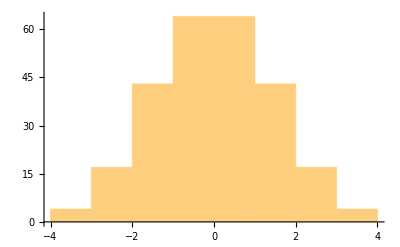

```mathematica
Histogram[iv]
```

```mathematica
q=4
```

4

```mathematica
J=4
```

4

```mathematica
Jm =RandomVariate[NormalDistribution[0,Sqrt[J^2   * ((q-1)!)/(S^(q-1))]],{S,S,S,S}]
```

```mathematica
Dynamic[{i1,i2,i3,i4}]
Ham=I^(q/2)Sum[ψ[i1,i2].Sum[ Jm[[i1,i2,i3,i4]]*ψ[i3,i4],{i3,i2+1,S},{i4,i3 + 1, S}],{i1,S-3},{i2,i1 + 1, S-2}]//Normal;
```

```mathematica
Ham
```

```mathematica
ivv = Ham//N//Eigenvalues//Sort
```

{-3.33276,-3.23499,-3.15533,-3.10792,-3.05016,-3.04538,-2.9689,-2.90137,-2.8738,-2.87041,-2.84396,-2.77888,-2.69117,-2.65069,-2.63791,-2.63019,-2.55147,-2.53328,-2.53068,-2.52705,-2.46628,-2.44616,-2.44529,-2.38079,-2.37163,-2.31141,-2.29816,-2.26001,-2.22951,-2.22043,-2.19211,-2.12449,-2.07163,-2.05704,-2.04792,-2.02475,-2.00945,-2.00649,-1.9963,-1.98875,-1.93858,-1.92729,-1.90926,-1.81507,-1.79116,-1.75904,-1.7431,-1.74018,-1.73631,-1.71694,-1.66608,-1.65035,-1.63998,-1.62041,-1.59851,-1.54358,-1.53677,-1.50217,-1.48338,-1.46957,-1.46663,-1.43754,-1.37868,-1.36624,-1.32142,-1.2996,-1.27843,-1.26248,-1.23366,-1.23049,-1.21048,-1.17875,-1.15324,-1.14574,-1.12234,-1.10099,-1.07923,-1.05996,-0.982815,-0.943402,-0.942043,-0.923144,-0.918422,-0.896242,-0.885381,-0.853893,-0.843338,-0.799364,-0.788159,-0.775598,-0.761739,-0.754585,-0.737783,-0.70494,-0.655101,-0.620534,-0.619709,-0.606768,-0.586663,-0.582109,-0.535907,-0.516392,-0.503242,-0.494346,-0.488686,-0.46503,-0.457685,-0.422438,-0.400702,-0.360453,-0.345464,-0.321141,-0.309486,-0.295546,-0.264774,-0.251672,-0.222912,-0.201195,-0.193909,-0.169172,-0.158222,-0.107315,-0.10258,-0.072272,-0.0664912,-0.0504468,-0.0484895,-0.000988025,0.0169601,0.0684256,0.068673,0.0756012,0.108658,0.116786,0.120678,0.138239,0.190596,0.201141,0.221143,0.274652,0.275144,0.290589,0.360889,0.361468,0.368439,0.37546,0.385965,0.435415,0.456338,0.489348,0.518695,0.541665,0.546461,0.564923,0.586721,0.59525,0.598756,0.639223,0.658068,0.691891,0.692301,0.712851,0.747832,0.756745,0.805041,0.824166,0.833017,0.837327,0.877708,0.881413,0.893244,0.950015,0.958542,0.97163,0.988473,1.01862,1.02326,1.04089,1.04564,1.0682,1.12411,1.13147,1.16224,1.1681,1.25166,1.25246,1.27605,1.2803,1.30357,1.31092,1.33797,1.34476,1.36949,1.40628,1.43226,1.49325,1.51066,1.51893,1.53172,1.53535,1.57485,1.59024,1.61706,1.63252,1.68677,1.69959,1.70346,1.7103,1.75038,1.75709,1.76902,1.86266,1.86595,1.87137,1.89228,1.92196,1.9501,1.96127,1.96694,2.01841,2.02669,2.04291,2.04802,2.05546,2.09887,2.1294,2.13222,2.19941,2.21868,2.26349,2.299,2.35836,2.37707,2.38592,2.39886,2.42223,2.44632,2.46041,2.49716,2.50417,2.54667,2.56745,2.60552,2.62677,2.67535,2.70614,2.71174,2.74798,2.77249,2.81888,2.86558,2.88816,3.02493,3.0381,3.10279,3.11103}

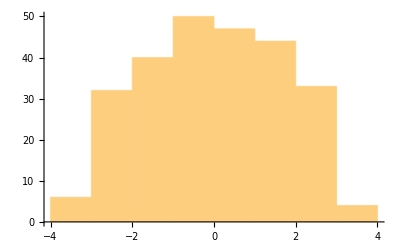

```mathematica
ivv //Histogram
```

Two Point functions

```mathematica
β =5;
H = Ham //N
```

```mathematica
Clear[Gn];
Gn[a_,b_,τ_,β_, λ_]:=Gn[a,b,τ,β ,λ]= Block[{ },
If[τ>0,
Eτ = MatrixExp[-τ H  λ ];
Eβτ = MatrixExp[(-β + τ) H λ];
(Tr[Eβτ.ψ[a].Eτ.ψ[b]]) / (Tr[Eβτ.Eτ]),

Eτ = MatrixExp[+τ H λ];
Eβτ = MatrixExp[(-β - τ) H λ];
-(Tr[Eβτ.ψ[b].Eτ.ψ[a]]) / (Tr[Eβτ.Eτ]),
]
]
```

```mathematica
Gn[1,1,1/4,1,1]
```

0.403082+8.148×10^-19 ⅈ

```mathematica
Dynamic[tt]
Gn[1,1,1,1,1]
```

0.5+1.20371×10^-35 ⅈ

```mathematica
tbGG =Table[{tt,Gn[1,1,tt,1,1]},{tt,-1/2,1/2,1/10}]//Re
```

{{-1/2,-0.375894},{-2/5,-0.38009},{-3/10,-0.393027},{-1/5,-0.415795},{-1/10,-0.450387},{0,-0.5},{1/10,0.450387},{1/5,0.415795},{3/10,0.393027},{2/5,0.38009},{1/2,0.375894}}

```mathematica
plt = ListPlot[tbGG,Joined->True]
```

-Graphics-

```mathematica
Spec[τ_,β_]:=Spec[τ,β ]= Block[{ },
If[τ>0,
Zβτm = Tr[MatrixExp[(-β * H)-(I*H*τ)]];
Zβτp = Tr[MatrixExp[(-β * H)+(I*H*τ)]];
Zβ = Tr[MatrixExp[(-β * H )]];
Abs[((Zβτm  *Zβτp )/(Zβ )^2)]
]
]
```

```mathematica
Spec[3,1]
```

0.0384954

```mathematica
tbSpec =Table[{tt,Spec[tt,10]},{tt,1,100,1}];
```

```mathematica
tap=Table[{i,Sum[tbSpec[[i]][[2]],{i,1,i}]},{i,1,100,1}];
```

```mathematica
pltSpec = ListPlot[Log[tbSpec],Joined->True]
```

-Graphics-

```mathematica
pltSpec2 = ListPlot[tap,Joined->True]
```

-Graphics-

GRAVITY CALLS

```mathematica
s0=1
ρ[M_]:=ρ[M]=Exp[s0] * Sinh[(2* Pi*Sqrt[2*M])/(2*Pi^2)];
```

1

```mathematica
corrJT[τ_,β_]:=corrJT[τ,β]= Block[{ },
If[τ>0,
ZβJ = Integrate[ρ[M]*Exp[-1*β*M],{M,0,Infinity}];
ZβαJTp= Integrate[ρ[M]*Exp[(-β * M)+(I*M*τ)],{M,0,Infinity}];
ZβαJTm = Integrate[ρ[M]*Exp[(-β * M)-(I*M*τ)],{M,0,Infinity}];
Abs[( (ZβαJTp *ZβαJTm )/((ZβJ )^2))]
]
]
```

```mathematica
ZβJ = Integrate[ρ[M]*Exp[-1*β*M],{M,0,Infinity}];
```

```mathematica
JTspectMa =Table[{tt,corrJT[tt,1]},{tt,1,10,1}]//N
```

{{1.,0.336088},{2.,0.0824788},{3.,0.0288667},{4.,0.0129692},{5.,0.00684273},{6.,0.00402609},{7.,0.00256107},{8.,0.00172705},{9.,0.00121846},{10.,0.000891149}}

```mathematica
ListLinePlot[JTspectMa, Mesh -> All, AxesOrigin -> {0, 0}]
```

-Graphics-